0.409339-1.20206 x-14.2227 x^2+353.301 x^3-511.616 x^4-18149.2 x^5+90535.2 x^6+146549. x^7-2.11185×10^6 x^8+4.07313×10^6 x^9+1.09292×10^7 x^10-5.9539×10^7 x^11+7.02312×10^7 x^12+1.41158×10^8 x^13-5.75419×10^8 x^14+7.0448×10^8 x^15+1.18301×10^8 x^16-1.66938×10^9 x^17+2.80012×10^9 x^18-2.69676×10^9 x^19+1.71506×10^9 x^20-7.36123×10^8 x^21+2.06553×10^8 x^22-3.43718×10^7 x^23+2.58003×10^6 x^24

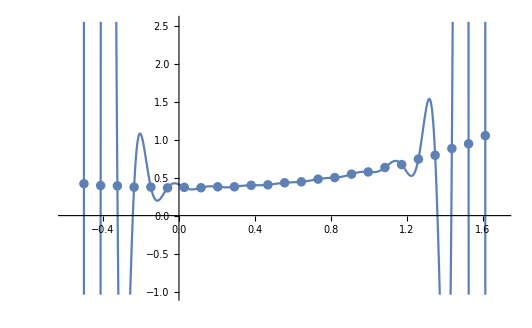

0.409339-1.20206 x-14.2227 x^2+353.301 x^3-511.616 x^4-18149.2 x^5+90535.2 x^6+146549. x^7-2.11185×10^6 x^8+4.07313×10^6 x^9+1.09292×10^7 x^10-5.9539×10^7 x^11+7.02312×10^7 x^12+1.41158×10^8 x^13-5.75419×10^8 x^14+7.0448×10^8 x^15+1.18301×10^8 x^16-1.66938×10^9 x^17+2.80012×10^9 x^18-2.69676×10^9 x^19+1.71506×10^9 x^20-7.36123×10^8 x^21+2.06553×10^8 x^22-3.43718×10^7 x^23+2.58003×10^6 x^24

-Graphics-

0.371558-5.48705×10^-6 x+0.185753 x^2+0.000311647 x^3+0.0306578 x^4-0.00252645 x^5+0.00733284 x^6-0.00171426 x^7-0.0160327 x^8+0.0268841 x^9-0.0200954 x^10+0.00734489 x^11-0.00107056 x^12

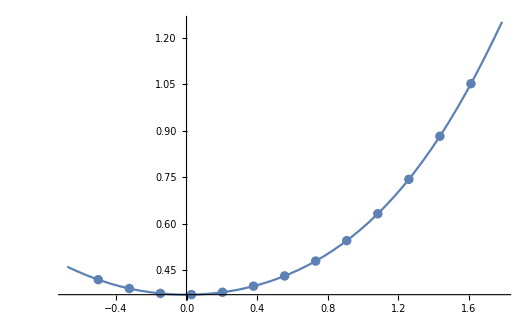

0.370259+0.0841686 x-0.166578 x^2-0.886014 x^3+4.30567 x^4-1.66242 x^5-9.61386 x^6+14.5814 x^7-7.99199 x^8+1.55599 x^9

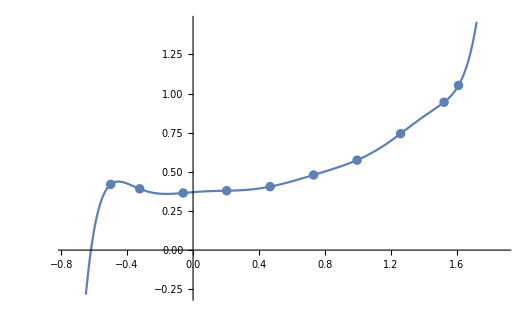

0.365964-0.0309764 x+0.24949 x^2+0.0883054 x^3-0.166707 x^4+0.07753 x^5

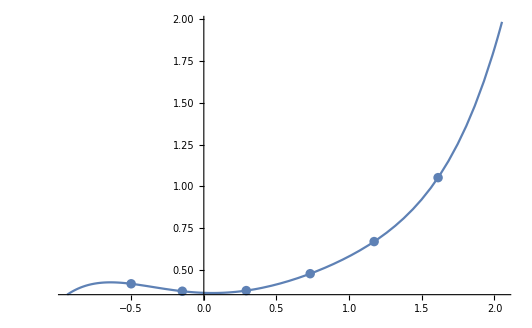

```mathematica
(*Вариант 4*)
(*Задание 1*)
data = {{-0.5,0.419945},{-0.412,0.395988},{-0.324,0.391402},{-0.236,0.374437},{-0.148,0.375642},{-0.06,0.364857},{0.028,0.371704},
{0.116,0.366656},{0.204,0.379343},{0.292,0.379343},{0.38,0.399032},{0.468,0.405545},{0.556,0.43196},{0.644,0.444969},{0.732,0.480039},
{0.82,0.500438},{0.908,0.545871},{0.996,0.574811},{1.084,0.632645},{1.172,0.67142},{1.26,0.743887},{1.348,0.793733},{1.436,0.882993},
{1.524,0.944755},{1.612,1.05247}};
h=data[[2,1]]-data[[1,1]];
(*Для начала построим интерполяционный многочлен при помощи встроенных средств*)
intrpl:=InterpolatingPolynomial[data,x];
Collect[intrpl,x]
gr1:=Plot[intrpl,{x,data[[1,1]]-h,data[[25,1]]+h}];
gr2:=ListPlot[data];
Show[{gr1,gr2}]
(*Задание 1*)
(*Будем использовать интерполяционные многочлены Лагранжа*)
(*n=25*)
n=Length[data]-1;
Array[xdata,{n+1,0}]; Array[ydata,{n+1,0}];
For[i =0,i<=n,i++, xdata[i]=data[[i+1,1]];
ydata[i]=data[[i+1,2]];
];
pln=∑_(i=0)^n ydata[i]×∏_(j=0)^n If[i!=j,(x-xdata[j])/(xdata[i]-xdata[j]),1];
lgr2[x_]:=Collect[pln,x];
lgr2[x]
gr1:=Plot[lgr2[x],{x,data[[1,1]]-h,data[[25,1]]+h}];
gr2:=ListPlot[data];
Show[{gr1,gr2}]
(*n=12,только нечётные узлы, но первый и последний узел учавствуют в любом случае*)
data2={};
For[i=1,i<=Length[data],i=i+2,
elem=data[[i]];
data2=Append[data2,elem]];
n=Length[data2]-1;
h=data2[[2,1]]-data2[[1,1]];
Array[xdata,{n+1,0}]; Array[ydata,{n+1,0}];
For[i =0,i<=n,i++, xdata[i]=data2[[i+1,1]];
ydata[i]=data2[[i+1,2]];
];
pln=∑_(i=0)^n ydata[i]×∏_(j=0)^n If[i!=j,(x-xdata[j])/(xdata[i]-xdata[j]),1];
lgr2[x_]:=Collect[pln,x];
lgr2[x]
gr1:=Plot[lgr2[x],{x,data2[[1,1]]-h,data2[[13,1]]+h}];
gr2:=ListPlot[data2];
Show[{gr1,gr2}]
(*берём значение многочлена в каждом 3-ем узле, но первый и последний узел также будут учавствовать*)
data3={{-0.5,0.419945}};
For[i=3,i<=Length[data],i=i+3,
elem=data[[i]];
data3=Append[data3,elem]];
data3=Append[data3,data[[25]]];
n=Length[data3]-1;
h=data3[[3,1]]-data3[[2,1]];
Array[xdata,{n+1,0}]; Array[ydata,{n+1,0}];
For[i =0,i<=n,i++, xdata[i]=data3[[i+1,1]];
ydata[i]=data3[[i+1,2]];
];
pln=∑_(i=0)^n ydata[i]×∏_(j=0)^n If[i!=j,(x-xdata[j])/(xdata[i]-xdata[j]),1];
lgr2[x_]:=Collect[pln,x];
lgr2[x]
gr1:=Plot[lgr2[x],{x,data3[[1,1]]-h,data3[[10,1]]+h}];
gr2:=ListPlot[data3];
Show[{gr1,gr2}]
(*берём значение многочлена в каждом 5-ом узле, но первый и последний узел также будут учавствовать*)
data4={{-0.5,0.419945}};
For[i=5,i<=Length[data],i=i+5,
elem=data[[i]];
data4=Append[data4,elem]];
n=Length[data4]-1;
h=data4[[3,1]]-data4[[2,1]];
Array[xdata,{n+1,0}]; Array[ydata,{n+1,0}];
For[i =0,i<=n,i++, xdata[i]=data4[[i+1,1]];
ydata[i]=data4[[i+1,2]];
];
pln=∑_(i=0)^n ydata[i]×∏_(j=0)^n If[i!=j,(x-xdata[j])/(xdata[i]-xdata[j]),1];
lgr2[x_]:=Collect[pln,x];
lgr2[x]
gr1:=Plot[lgr2[x],{x,data4[[1,1]]-h,data4[[6,1]]+h}];
gr2:=ListPlot[data4];
Show[{gr1,gr2}]
```